```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]

fs=Style[#,FontSize->14]&;
```

peeters`

/Users/pjoot/project/figures/phy487-qmsolids

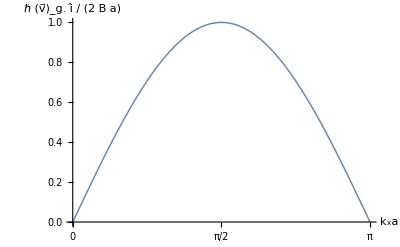

```mathematica
Clear[p]
p = Plot[ Sin[x]
, {x, 0, Pi}
, Ticks -> { {0, Pi/2,Pi}, Automatic }
, PlotStyle->Thick
, AxesLabel->fs/@{"k_xa","ℏ (v⃗)_g. î / (2 B a)" }
]
```

```mathematica
peeters`exportForLatex["qmSolidsPs9P2cFig1", p]
```

{qmSolidsPs9P2cFig1.eps,qmSolidsPs9P2cFig1pn.png}

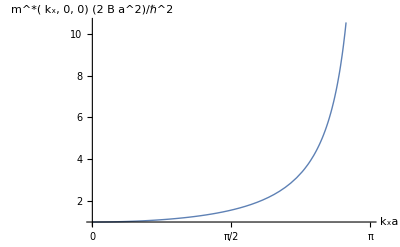

```mathematica
ClearAll[p]
p = Plot[ u/Sin[u]
, {u, 0, Pi}
, Ticks -> {{0, Pi/2, Pi}, Automatic }
, PlotStyle->Thick
, AxesLabel->fs/@{ "k_xa","m^*( k_x, 0, 0) (2 B a^2)/ℏ^2" }
(*, PlotRange -> Full*)
]
```

```mathematica
peeters`exportForLatex["qmSolidsPs9P2dFig1", p]
```

{qmSolidsPs9P2dFig1.eps,qmSolidsPs9P2dFig1pn.png}

```mathematica
(*Integrate[Sin[x], {x, 0, Pi/2}]*)
```